# Dynamical Analysis of evolved ANN

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";

SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## CTRNN Definition

### Differential equations

General definition of the two-node network, and specialization via replacement rules.

```mathematica
σ[x_]=1/(1+ⅇ^-x);

maxp = 20;
maxy =60;

neuron= DynamicalSystem[
{(-y+w σ[y+θ]+J)/τ},
{{y,-maxy,maxy}},
{{w,-maxp,maxp},
{θ,-maxp,maxp},
{J,-maxy,maxy},
{τ,0.5,20}}];

couple =DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+J)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-maxp,maxp},{y2,-maxp,maxp}},
{{w11,-maxp,maxp},{w12,-maxp,maxp},{w21,-maxp,maxp},{w22,-maxp,maxp},{θ1,-maxp,maxp},{θ2,-maxp,maxp},{τ1,0.5,20},{τ2,0.5,20},{J,-50,50}}];
```

### Specialization

```mathematica
output1 = neuron/.{w->-8.81319,θ->3.19778,τ->1.0,J->0};
output2 = neuron/.{w->-6.1908,θ->3.79052,τ->1.0,J->0};
inW=9.79266;

network = couple/.{w11->7.54563,w21->0,w12->-2.07816, w22->0.0,θ1->-4.0057,θ2->1.57389,τ1->1.0,τ2->1.0,J->0};
With[{ε=10^-7},networko=TransformDynamicalSystem[network,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
With[{ε=10^-7},output1o=TransformDynamicalSystem[output1,{{o,ε,1-ε}},{σ[y+θ]}]];
With[{ε=10^-7},output2o=TransformDynamicalSystem[output2,{{o,ε,1-ε}},{σ[y+θ]}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

### Output neuron phase portraits

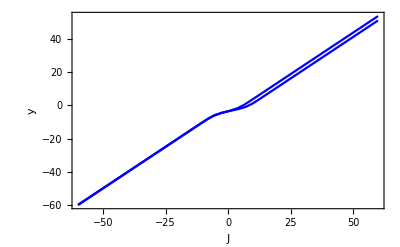

```mathematica
input=0;

(*EquilibriumPoints[output/.J->0.0]*)
(*Manipulate[EquilibriumPoints[output/.J->input], {input,-10,10}]*)

(*DisplayPhasePortrait[output/.J->input]*)
o1m=Manipulate[GraphicsColumn[{DisplayPhasePortrait[output1/.J->input],DisplayPhasePortrait[output2/.J->input]}],{input,-10,10},Paneled->false,FrameLabel->"O12"]

Show[DisplayBifurcationDiagram[output1,J],DisplayBifurcationDiagram[output2,J]]
```

### Hidden neuron bifurcation diagram

```mathematica
(*bifPl=DisplayBifurcationDiagram[hidden,J,GridLinesStyle->Dashed,GridLines->{{0},{0}}];
$BifurcationDiagramBPs

(* Overlay actual trajectories *)
duration=5;
startAt=0;
SetStartEnd[1];
phPlN1F=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2F=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl1=Show[bifPl,phPlN1F,PlotRange->{{-10,15},{-1,14}},PlotLabel->"Centre",AspectRatio->1.0];

SetStartEnd[2];
phPlN1A=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2A=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl2=Show[bifPl,phPlN1A,PlotRange->{{-1.5,1},{-1,8}},PlotLabel->"Avoidance",AspectRatio->1.0];

(* Show detail of avoidance behaviour, and long-term return to gaussian *)
duration=10.0;SetStartEnd[2];
phPlN1AFull=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
bifPhPl2Full=Show[bifPl,phPlN1AFull,PlotRange->{{-3,7},{0,14}},PlotLabel->"Avoidance and Return",AspectRatio->1.0];

GraphicsRow[{bifPhPl1,bifPhPl2,bifPhPl2Full},ImageSize->800]
*)
```